### ED

```mathematica
184756^2
```

34134779536

```mathematica
(* Input *)
(* set Length of chain *)
L=10;
(* set boundary condition: 0 for periodic; 1 for open boundary *)
bdry=1;
δJ=0.1;
(* end of Input *)
randJ=Array[1+δJ 2 (RandomReal[1]-0.5)&,L]
(* construct Hamiltonian in Subscript[S, tot]^z=0 (even chain) or 1/2 (odd chain) subspace *)
state=Select[Range[2^L-1],Total@IntegerDigits[#,2,L]==Ceiling[L/2]+0&];
dim=Length@state;
mat=Table[0.,{i,dim},{j,dim}];
Do[
sz=IntegerDigits[state[[j]],2,L];
Do[
fsz=sz;
If[sz[[i]]+sz[[Mod[i+1,L,1]]]==1,
fsz[[i]]=Abs[sz[[i]]-1];fsz[[Mod[i+1,L,1]]]=Abs[sz[[Mod[i+1,L,1]]]-1];
pos=Position[state,FromDigits[fsz,2]][[1,1]];
mat[[j,pos]]=0.5 randJ[[i]];
],{i,L-bdry}];
ele=0;sz=sz-0.5;
Do[ele+=randJ[[i]]sz[[i]]sz[[Mod[i+1,L,1]]],{i,L-bdry}];
mat[[j,j]]=ele;
,{j,dim}]
(*diagonalization*)
{val,u}=Eigensystem[mat];
gs=Position[val,Min[val]][[1,1]];
Print["Dimension of H = " ,dim, "; ",If[bdry==0,"Periodic Boundary Condition", "Open Boundary Condition"],"
","Spin Gap in this sector = ", RankedMin[val,2]-Min[val]]
```

{1.08455,0.937427,1.09301,0.906762,0.955985,1.06266,1.04634,1.07015,1.07321,0.906877}

Dimension of H = 252; Open Boundary Condition
Spin Gap in this sector = 0.369101

Dimension of H = 252; Open Boundary Condition
Spin Gap in this sector = 0.327362

```mathematica
6.91174-6.69246
6.02672466186217-5.780492604462401
```

0.21928

0.246232

```mathematica
Min[val]
```

-6.02672

```mathematica
(* 
calculate <Subscript[S, i]^z(t)Subscript[S, j]^z>, j is the reference site at the center of chain;
I set Δτ=0.1, total Time=50;
*)
evol=Array[0&,L];szvec=Table[0.,{i,dim}];
Do[
sz=IntegerDigits[state[[j]],2,L];
szvec[[j]]=sz[[Ceiling[L/2]]]-0.5;
,{j,dim}];
myvecr=u.(u[[gs]]*szvec);
Do[
szvec=Table[0.,{i,dim}];
Do[
sz=IntegerDigits[state[[j]],2,L];
szvec[[j]]=sz[[site]]-0.5;
,{j,dim}];
myvecl=u.(u[[gs]]*szvec);
evol[[site]]=Table[{site,τ,Total[myvecl*Exp[ⅈ val τ]*myvecr]*Exp[-ⅈ val[[gs]] τ](*-Total[myvecl*myvecr]*)},{τ,0,500,0.1}];
,{site,L}]
Print["reference site = ", Ceiling[L/2], ", Total evolution Time = 50, Time Interval = 0.1"]
```

reference site = 7, Total evolution Time = 50, Time Interval = 0.1

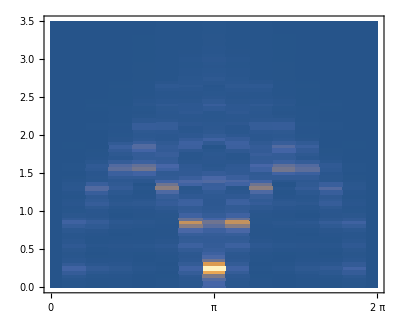

```mathematica
(* calculate S(ω,q) from <Subscript[S, i]^z(t)Subscript[S, j]^z> *)
(* Integrate τ, I set damping = 0.1 *)
rdat=Table[{site,ω,Re[2π /Length[evol[[site]]]2Exp[(ⅈ ω-0.05)*evol[[site,;;,2]]].Re@evol[[site,;;,3]]]},{site,1,L},{ω,0.0,3.5,0.05}];
(* Fourier transformation to k space *)
wqdat=Table[{q,rdat[[1,j,2]],Abs[ 2π /Length@rdat[[;;,j]] Exp[-ⅈ q (rdat[[;;,j,1]]-Ceiling[L/2])].rdat[[;;,j,3]]]},{j,Length@rdat[[1,;;,2]]},{q,0,2π,2π/L}];
ListDensityPlot[Flatten[wqdat,1],PlotRange->{All,All,All},AspectRatio->0.8,PlotLegends->Automatic,FrameTicks->{{-π/2,-π,0,π/2,π,3π/2,2π},Automatic},InterpolationOrder->0]
```

```mathematica
1.57/0.246
```

6.38211

```mathematica
6.38 9.4
```

59.972

```mathematica
Sort@val
```

{-1.9514,-1.49273,-1.18393,-0.993511,-0.693275,-0.577057,-0.400969,-0.288987,-0.261473,-0.12349,0.127215,0.277479,0.588805,0.589936,0.722521,0.800729,1.04591,1.12349,1.28977,1.40097,1.5}

{-2.83624,-2.2789,-1.9514,-1.79046,-1.49273,-1.46232,-1.18393,-1.13315,-0.993511,-0.793179,-0.784716,-0.693275,-0.577057,-0.479578,-0.400969,-0.288987,-0.281966,-0.261473,-0.12349,-0.0367994,0.127215,0.277479,0.279235,0.474046,0.588805,0.589936,0.722521,0.800729,0.96216,1.04591,1.12349,1.16188,1.28977,1.40097,1.5}

{-2.002,-1.42146,-1.01421,-0.872789,-0.616025,-0.485342,-0.25,0.0429989,0.25,0.382357,0.656803,0.75,0.963635,1.11603,1.25}

```mathematica
data={{4,1.616025403784435-0.9571067811865448},{6,2.4935771338879222-2.001995356898532},{8,3.374932598687889-2.982240487762886},{10,4.258035207282882-3.9306735895015454},{12,5.142090632840528-4.861147937036377},{14,6.02672466186217-5.780492604462401},{16,6.91174-6.69246},{18,7.79701-7.59928},{20,8.682473-8.502379},{22,9.568076-9.402679},{24,10.45379-10.30083},{26,11.33958-11.19730},{28,12.22544-12.09243},{30,13.11136-12.98645},{40,17.54146-17.44562},{50,21.97204-21.89424},{60,26.40302-26.33739},{70,30.83400-30.77733},{80,35.26483-35.21523}};
```

FittedModel[-1.2121-0.0246337 x]

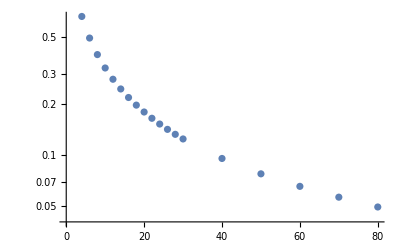

```mathematica
fit=LinearModelFit[{N@#[[1]],Log@#[[2]]}&/@data[[5;;]],x,x]
Show[ListLogPlot[data[[;;]]]]
```

FittedModel[1.02228-0.914826 x]

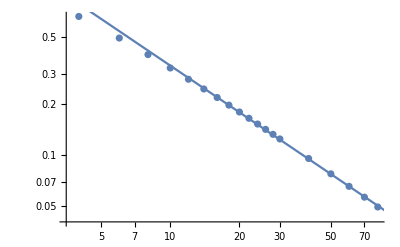

```mathematica
fit=LinearModelFit[Log@data[[5;;]],x,x]
Show[ListLogLogPlot[data[[;;]]],Plot[fit[x],{x,0,100}]]
```

```mathematica
Exp[1.022275570985518-0.9148257468166539 Log[x]]
```

2.77951/x^0.914826

```mathematica
π/2.
```

1.5708

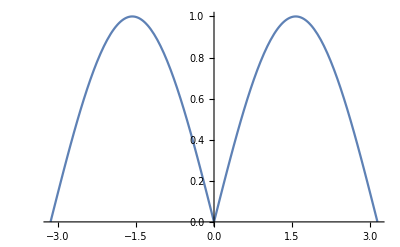

```mathematica
Show[Table[Plot[N@Cos[q1]+N@Cos[q-q1],{q,-π/2+q1,π/2+q1}],{q1,-π/2,π/2,π}],PlotRange->All]
```

```mathematica
Simplify[Cos[q]+Cos[π/2-q]]
```

Cos[q]+Sin[q]

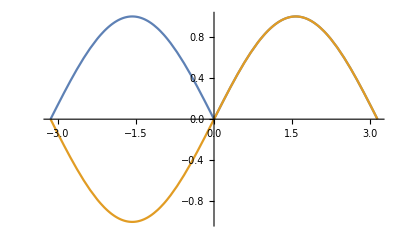

```mathematica
Plot[{Abs[Sin[q]],Cos[π/2]+Cos[q-π/2]},{q,-π,π}]
```

```mathematica
MatrixExp[θ/2 {{0,-1},{1,0}}]
```

{{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}